```mathematica
Needs["MFGraphs`"]
```

```mathematica
Get["/Users/ribeirrd/Dropbox/My Mac (kl-14835.kaust.edu.sa)/Documents/workspace/MFGraphs/MFGraphs/MFGraphs.m"](*Ricardo, use this when not running from eclipse.*)
```

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,DataG,DataToEquations,EqEliminatorX,F,FixedPointSolverStepX,FixedSolverStepX2,g,g$2733,H,I1,I2,Intg,m,m$,n,OtherWay,p,Parameters,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,StartSolverX,Test,TransitionsAt,triple2path,U1,U2,V,V$2733,W,W$2733,x,x$}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[17];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

Something is wrong with the equations: (u163<1&&u162==2&&j132==2&&u157==u161&&u156==u161&&jt149==0)||(u163==1&&((u162<2&&j132==0&&u157==u161&&u156==u161&&jt149==0)||(u162==2&&0≤j132≤2&&u157==u161&&u156==u161&&jt149==0)))

DataToEquations: Critical case ...

Something is wrong with the equations: (-2+j132+u157<1&&-j132+u156==2&&j132==2&&u157==-2+u155&&u156==-2+u155&&jt149==0)||(-2+j132+u157==1&&((-j132+u156<2&&j132==0&&u157==-2+u155&&u156==-2+u155&&jt149==0)||(-j132+u156==2&&0≤j132≤2&&u157==-2+u155&&u156==-2+u155&&jt149==0)))

DataToEquations: Reducing ...

EqEliminatorX: Reached a solution!

DataToEquations: Done.

#### Non-linear case

```mathematica
MFGEquations["reduced"][[2]]//KeySort
```

<|j131→2,j133→2-j132,j134→j132,j135→2-j132,j136→2,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→j132+jt149,jt146→2-j132-jt149,jt147→-jt149,jt148→jt149,jt150→-jt149,jt151→j132,jt152→0,jt153→2-j132,jt154→0,u158→2,u159→1,u160→u155,u164→2,u165→1,u166→u155|>

```mathematica
MFGEquations["criticalreduced"][[2]]//KeySort
```

<|j131→2,j132→1/2,j133→2-1/2,j134→1/2,j135→2-1/2,j136→2,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→1/2+0,jt146→2-1/2-0,jt147→-0,jt148→0,jt149→0,jt150→-0,jt151→1/2,jt152→0,jt153→2-1/2,jt154→0,u155→9/2,u156→5/2,u157→5/2,u158→2,u159→1,u160→9/2,u161→-2+9/2,u162→-1/2+5/2,u163→-2+1/2+5/2,u164→2,u165→1,u166→9/2|>

```mathematica
nsol=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],20]
```

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

<|j136→2,u164→2,u165→1,j131→2,j133→2-0.325275,j134→0.325275,j135→2-0.325275,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→0.325275+0,jt146→2-0.325275-0,jt147→-0,jt148→0,jt150→-0,jt151→0.325275,jt152→0,jt153→2-0.325275,jt154→0,u158→2,u159→1,u166→4.17257,u160→4.17257,u161→-1.67538+1. 4.17257,u162→-0.171919-1. 0.325275+1. 2.49719,u163→-1.82247+1. 0.325275+1. 2.49719,j132→0.325275,jt149→0,u155→4.17257,u156→2.49719,u157→2.49719|>

```mathematica
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]]<10^(-9)/.nsol
```

True

```mathematica
MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.nsol
```

{0.,-1.66533×10^-16,2.22045×10^-16}

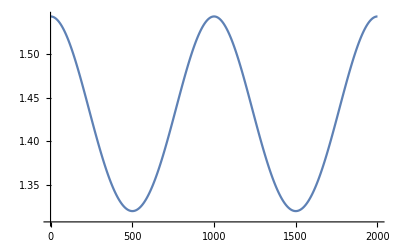

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.

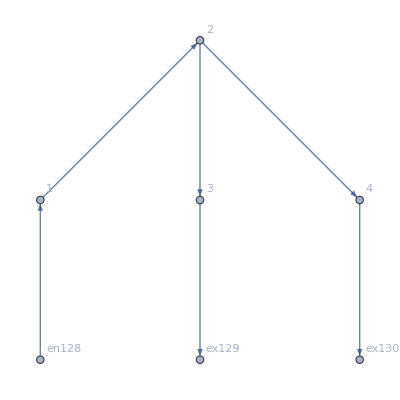
<|FG→-Graphics-,EqAllAll→NonNegative[j131]&&NonNegative[j132]&&NonNegative[j133]&&NonNegative[j134]&&NonNegative[j135]&&NonNegative[j136]&&NonNegative[j137]&&NonNegative[j138]&&NonNegative[j139]&&NonNegative[j140]&&NonNegative[j141]&&NonNegative[j142]&&NonNegative[jt143]&&NonNegative[jt144]&&NonNegative[jt145]&&NonNegative[jt146]&&NonNegative[jt147]&&NonNegative[jt148]&&NonNegative[jt149]&&NonNegative[jt150]&&NonNegative[jt151]&&NonNegative[jt152]&&NonNegative[jt153]&&NonNegative[jt154]&&j137==jt143&&j136==jt144&&j131==jt145+jt146&&j138==jt147+jt148&&j139==jt149+jt150&&j132==jt151&&j140==jt152&&j133==jt153&&j141==jt154&&j131==jt144&&j142==jt143&&j137==jt147+jt149&&j132==jt145+jt150&&j133==jt146+jt148&&j138==jt152&&j134==jt151&&j139==jt154&&j135==jt153&&j136==2&&u164==2&&u165==1&&NonNegative[u155-u166]&&NonNegative[-u156+u161]&&NonNegative[-u157+u161]&&NonNegative[u156-u161]&&NonNegative[u156-u157]&&NonNegative[u157-u161]&&NonNegative[-u156+u157]&&NonNegative[u158-u162]&&NonNegative[u159-u163]&&-u160+u166==0&&-u158+u164==0&&-u159+u165==0&&(j137==0||j131==0)&&(j138==0||j132==0)&&(j139==0||j133==0)&&(j140==0||j134==0)&&(j141==0||j135==0)&&(j142==0||j136==0)&&(jt143==0||jt144==0)&&(jt145==0||jt147==0)&&(jt146==0||jt149==0)&&(jt148==0||jt150==0)&&(jt151==0||jt152==0)&&(jt153==0||jt154==0)&&jt143==0&&(jt144==0||-u155+u166==0)&&(jt145==0||-u156+u161==0)&&(jt146==0||-u157+u161==0)&&(jt147==0||u156-u161==0)&&(jt148==0||u156-u157==0)&&(jt149==0||u157-u161==0)&&(jt150==0||-u156+u157==0)&&(jt151==0||-u158+u162==0)&&jt152==0&&(jt153==0||-u159+u163==0)&&jt154==0,reduced→{(u163<1&&u162==2&&j132==2&&u157==u161&&u156==u161&&jt149==0)||(u163==1&&((u162<2&&j132==0&&u157==u161&&u156==u161&&jt149==0)||(u162==2&&0≤j132≤2&&u157==u161&&u156==u161&&jt149==0))),<|j136→2,u164→2,u165→1,j131→2,j133→2-j132,j134→j132,j135→2-j132,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→j132+jt149,jt146→2-j132-jt149,jt147→-jt149,jt148→jt149,jt150→-jt149,jt151→j132,jt152→0,jt153→2-j132,jt154→0,u158→2,u159→1,u166→u155,u160→u155|>},Nlhs→{2-u155+u161,j132-u156+u162,2-j132-u157+u163},EqCriticalCase→2-u155+u161==0&&j132-u156+u162==0&&2-j132-u157+u163==0,criticalreduced→{True,<|j136→2,u164→2,u165→1,j131→2,j133→2-1/2,j134→1/2,j135→2-1/2,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→1/2+0,jt146→2-1/2-0,jt147→-0,jt148→0,jt150→-0,jt151→1/2,jt152→0,jt153→2-1/2,jt154→0,u158→2,u159→1,u166→9/2,u160→9/2,u161→-2+9/2,u162→-1/2+5/2,u163→-2+1/2+5/2,j132→1/2,jt149→0,u155→9/2,u156→5/2,u157→5/2|>},Nrhs→{0.324624,j132+Intg[j132],2-j132+Intg[2-j132]},EqGeneralCase→2-u155+u161==0.324624&&j132-u156+u162==j132+Intg[j132]&&2-j132-u157+u163==2-j132+Intg[2-j132]|>

```mathematica
MFGEquations
```

```mathematica
nsol
```

<|j136→2,u164→2,u165→1,j131→2,j133→2-0.325275,j134→0.325275,j135→2-0.325275,j137→0,j138→0,j139→0,j140→0,j141→0,j142→0,jt143→0,jt144→2,jt145→0.325275+0,jt146→2-0.325275-0,jt147→-0,jt148→0,jt150→-0,jt151→0.325275,jt152→0,jt153→2-0.325275,jt154→0,u158→2,u159→1,u166→4.17257,u160→4.17257,u161→-1.67538+1. 4.17257,u162→-0.171919-1. 0.325275+1. 2.49719,u163→-1.82247+1. 0.325275+1. 2.49719,j132→0.325275,jt149→0,u155→4.17257,u156→2.49719,u157→2.49719|>

```mathematica
Select[(-1.8224702815788614+1. j132+1. u157<1&&-0.17191949522867161-1. j132+1. u156==2&&j132==2&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0)||(-1.8224702815788614+1. j132+1. u157==1&&((-0.17191949522867161-1. j132+1. u156<2&&j132==0&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0)||(-0.17191949522867161-1. j132+1. u156==2&&0≤j132≤2&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0))), (Head[#]===Equal)&]
```

False

```mathematica
Reduce[(-1.8224702815788614+1. j132+1. u157<1&&-0.17191949522867161-1. j132+1. u156==2&&j132==2&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0)||(-1.8224702815788614+1. j132+1. u157==1&&((-0.17191949522867161-1. j132+1. u156<2&&j132==0&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0)||(-0.17191949522867161-1. j132+1. u156==2&&0≤j132≤2&&u157==-1.6753759312240248+1. u155&&u156==-1.6753759312240248+1. u155&&jt149==0)))]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

jt149==0&&u157==2.49719&&u156==2.49719&&u155==4.17257&&j132==0.325275